```mathematica
(*Params*)
r = .666; (*Prey Growth rate*)
a = .3; (*Search/attack efficiency*)
q = 1.; (*Predator mortality rate*)
c = .9; (*Conversion efficiency*)

(*Num solve*)
predprey = NDSolve[{P'[t]==c*a*P[t]*F[t]-q*P[t],F'[t]==r*F[t]-a*P[t]*F[t], P[0]==10,F[0]==20},{P,F},{t,20}]
```

{{P→InterpolatingFunction[…],F→InterpolatingFunction[…]}}

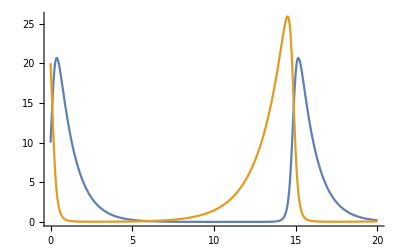

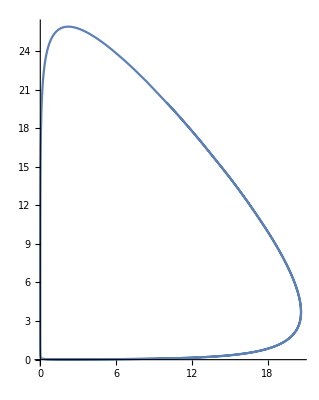

```mathematica
Plot[{Evaluate[P[t]/.predprey],Evaluate[F[t]/.predprey]},{t,0,20},PlotRange->All]
ParametricPlot[Evaluate[{P[t],F[t]}/.predprey],{t,0,20},PlotRange->All]
```

```mathematica
(*Params*)
a = .666; (*Prey Growth rate*)
b = 1.333; (*Search/attack efficiency*)
c = 1.; (*Predator mortality rate*)
d = 1.; (*Conversion efficiency*)

(*Num solve*)
predprey = NDSolve[{P'[t]==c*P[t]*F[t]-d*P[t],F'[t]==a*F[t]-b*P[t]*F[t], P[0]==.9,F[0]==1.8},{P,F},{t,20}]
```

{{P→InterpolatingFunction[…],F→InterpolatingFunction[…]}}

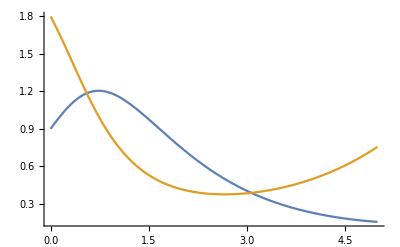

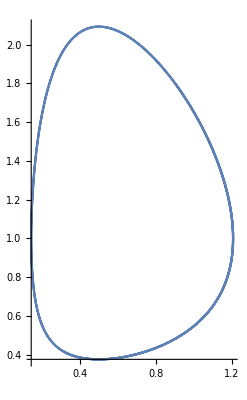

```mathematica
Plot[{Evaluate[P[t]/.predprey],Evaluate[F[t]/.predprey]},{t,0,5},PlotRange->All]
ParametricPlot[Evaluate[{P[t],F[t]}/.predprey],{t,0,20},PlotRange->All]
```